# DINO: Dynamical Inspection of Newtonian Orbits

### Autores del proyecto: E. Canul, A. A. Aroche, G. Urrutia-Sánchez, G. Martínez-Bautista Implementación en Mathematica: Carlos Manuel Rodríguez Martínez

Para más información leer el paper anexo.

Ecuaciones del modelo

```mathematica
Mb = 1293;
b = 1.52;
Md = 2155;
a = b/0.2;
ah = 22.25;
ρ = 0.258;
G = 1;

ax[x_,y_]:= -(G Mb x)/((x^2+y^2+b^2)^(3/2))-(G Md x)/((x^2+y^2+a^2)^(3/2))+4 π G ρ ah^2 (x/((x^2+y^2)(1+(√(x^2+y^2))/ah))-(ah x Log[1+(√(x^2+y^2))/ah])/((x^2+y^2)^(3/2)));
ay[x_,y_]:= -(G Mb y)/((x^2+y^2+b^2)^(3/2))-(G Md y)/((x^2+y^2+a^2)^(3/2))+4 π G ρ ah^2 (y/((x^2+y^2)(1+(√(x^2+y^2))/ah))-(ah y Log[1+(√(x^2+y^2))/ah])/((x^2+y^2)^(3/2)));

axclasico[x_,y_]:= -(G Mb x)/((x^2+y^2+b^2)^(3/2))-(G Md x)/((x^2+y^2+a^2)^(3/2));
ayclasico[x_,y_]:= -(G Mb y)/((x^2+y^2+b^2)^(3/2))-(G Md y)/((x^2+y^2+a^2)^(3/2));

VBulge[r_]:= √((G Mb r^2)/((r^2+b^2)^(3/2)));
VDisk[r_]:= √((G Md r^2)/((r^2+a^2)^(3/2)));
VHalo[r_]:= √(4 π G ρ ah^3 Abs[1/(ah(1+r/ah))-Log[1+r/ah]/r]);
VTotal[r_]:=√(VBulge[r]^2+VDisk[r]^2+VHalo[r]^2);
```

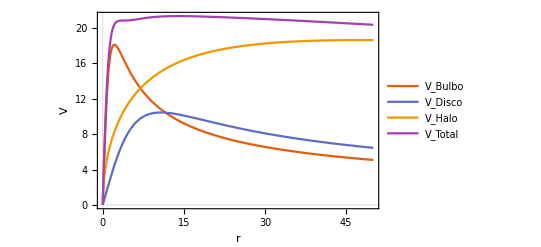

```mathematica
Plot[{VBulge[r],VDisk[r],VHalo[r],VTotal[r]},{r,0,50},PlotTheme->"Scientific",FrameLabel->{"r","V"},PlotLegends->{"V_Bulbo","V_Disco","V_Halo","V_Total"}]
```

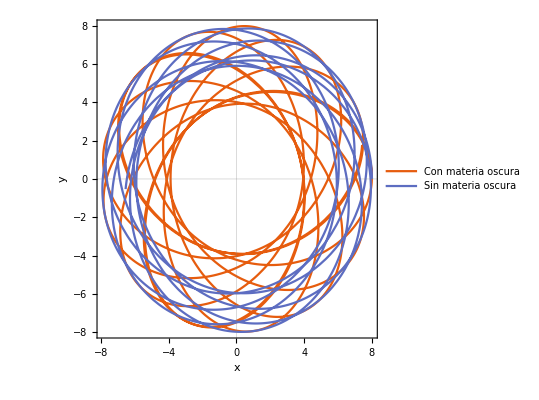

```mathematica
ri= 8;
vi = VTotal[ri];
sol = NDSolve[{x''[t] == ax[x[t],y[t]],y''[t] == ay[x[t],y[t]],x[0] == ri,x'[0] == 0,y[0] == 0,y'[0]==14},{x,y},{t,0,100}];

solclasica = NDSolve[{x''[t] == axclasico[x[t],y[t]],y''[t] == ayclasico[x[t],y[t]],x[0] == ri,x'[0] == 0,y[0] == 0,y'[0]==14},{x,y},{t,0,100}];

SetOptions[ParametricPlot,BaseStyle->{FontSize->14}];
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],Evaluate[{x[t],y[t]}/.solclasica]},{t,0,20},PlotTheme->"Scientific", FrameLabel->{"x","y"}, PlotLegends->{"Con materia oscura", "Sin materia oscura"}]
```

Gráfica interactiva

```mathematica
vi = 14;
solutions = {};
Do[
sol = NDSolve[{x''[t] == ax[x[t],y[t]],y''[t] == ay[x[t],y[t]],x[0] == ri,x'[0] == 0,y[0] == 0,y'[0]==14},{x,y},{t,0,100}];
AppendTo[solutions,First[sol]];
,{ri, 10,50,10}
];

SetOptions[ParametricPlot,BaseStyle->{FontSize->14}];
Manipulate[
ParametricPlot[
{
Evaluate[{x[t],y[t]}/.solutions[[1]]],
Evaluate[{x[t],y[t]}/.solutions[[2]]],
Evaluate[{x[t],y[t]}/.solutions[[3]]],
Evaluate[{x[t],y[t]}/.solutions[[4]]]
}
,{t,0,tmax},PlotTheme->"Scientific", FrameLabel->{"x","y"},PlotRange->{{-40,40},{-40,40}}]
,{{tmax,10},0.01,100},SaveDefinitions->True
]
```

```mathematica
anim =Table[
ParametricPlot[
{
Evaluate[{x[t],y[t]}/.solutions[[1]]],
Evaluate[{x[t],y[t]}/.solutions[[2]]],
Evaluate[{x[t],y[t]}/.solutions[[3]]],
Evaluate[{x[t],y[t]}/.solutions[[4]]]
}
,{t,0,tmax},PlotTheme->"Scientific", FrameLabel->{"x","y"},PlotRange->{{-40,40},{-40,40}}]
,{tmax,0.01,100,0.3}
];
Export["planetas.avi",anim]
```

planetas.avi

Más bonito

```mathematica
Positions[t_]:= Module[{},{
Evaluate[{x[t],y[t]}/.solutions[[1]]],
Evaluate[{x[t],y[t]}/.solutions[[2]]],
Evaluate[{x[t],y[t]}/.solutions[[3]]],
Evaluate[{x[t],y[t]}/.solutions[[4]]]
}];
Manipulate[
ParametricPlot[
Evaluate[Positions[t]]
,{t,0,tmax},
PlotRange->{{-40,40},{-40,40}},
Axes->False,
Background->Black,
Epilog->{PointSize[Large],White,Point[Positions[tmax]]},
PlotStyle->{ColorData["HTML"]["LightSteelBlue"], ColorData["HTML"]["CornflowerBlue"], ColorData["HTML"]["RoyalBlue"],ColorData["HTML"]["SteelBlue"]}
]
,{{tmax,10},0.01,100},SaveDefinitions->True
]
```

Y la animación

```mathematica
anim =Table[
ParametricPlot[
Evaluate[Positions[t]]
,{t,0,tmax},
PlotRange->{{-40,40},{-40,40}},
Axes->False,
Background->Black,
Epilog->{PointSize[Large],White,Point[Positions[tmax]]},
PlotStyle->{ColorData["HTML"]["LightSteelBlue"], ColorData["HTML"]["CornflowerBlue"], ColorData["HTML"]["RoyalBlue"],ColorData["HTML"]["SteelBlue"]}
]
,{tmax,0.01,100,0.3}
];
Export["planetas.avi",anim]
```

$Aborted

Animación 3D

```mathematica
CreatePoints[n_]:=Block[{pointsBulk,pointsHalo},
pointsBulk = RandomPoint[Ellipsoid[{0,0,0},10*{2,2,1.5}],n];
pointsHalo = RandomPoint[Ellipsoid[{0,0,0},10*{4,4,0.5}],3n/4];
Join[pointsBulk,pointsHalo]
];
```

```mathematica
ListPointPlot3D[CreatePoints[10000]]
```

-Graphics3D-

Cálculo del error

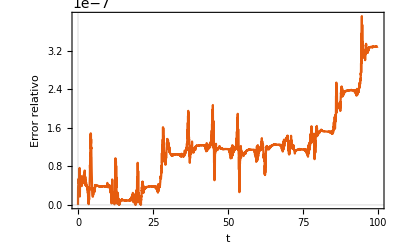

```mathematica
ϕdisco[x_,y_]:=-(G Md)/(√(x^2+y^2+a^2));
ϕbulbo[x_,y_]:=-(G Mb)/(√(x^2+y^2+b^2));
ϕhalo[x_,y_]:=-4 π G ρ ah^3 Log[1+(√(x^2+y^2))/ah]/(√(x^2+y^2));
ECin[vx_,vy_]:=1/2(vx^2+vy^2);
EPot[x_,y_]:= ϕdisco[x,y]+ ϕbulbo[x,y]+ ϕhalo[x,y];
E0 = Evaluate[(EPot[x[0],y[0]]+ECin[x'[0],y'[0]])/.sol][[1]];
Plot[Abs[E0-Evaluate[(EPot[x[t],y[t]]+ECin[x'[t],y'[t]])/.sol]]/Abs[E0],{t,0,100},PlotTheme->"Scientific",FrameLabel->{"t", "Error relativo"}]
```

```mathematica
Plot3D[EPot[x,y],{x,-30,30},{y,-30,30}]
```

-Graphics3D-

```mathematica
Plot3D[ϕhalo[x,y],{x,-30,30},{y,-30,30},PlotRange->Full]
```

-Graphics3D-

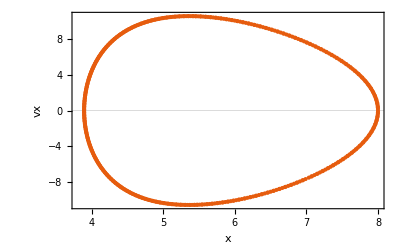

```mathematica
ri= 8;
poincare = Reap[NDSolve[{x''[t] == ax[x[t],y[t]],y''[t] == ay[x[t],y[t]],x[0] == ri,x'[0] == 0,y[0] == 0,y'[0]==14,WhenEvent[y[t] == 0 && y'[t] > 0,Sow[{x[t],x'[t]}]]},{x,y},{t,0,1000}]];
ListPlot[poincare[[2,1]], PlotTheme->"Scientific", FrameLabel->{"x ","vx"}]
```

```mathematica
f1[Rc_]:=1/(ah(1+Rc/ah))-Log[1+Rc/ah]/Rc;
f2[Rc_]:= Mb/((Rc^2+b^2)^(3/2))+Md/((Rc^2+a^2)^(3/2));
GetRc[v_]:=Rc /.FindRoot[Rc - √((v^2-4 π G ρ ah^3 f1[Rc])/(G f2[Rc])),{Rc,0.5}];
```

```mathematica
GetRc[14]
```

1.05127

```mathematica
ri= 8.0;
PS={};

Do[
poincare = Reap[NDSolve[{x''[t] == ax[x[t],y[t]],y''[t] == ay[x[t],y[t]],x[0] == ri,x'[0] == 0,y[0] == 0,y'[0]==14,WhenEvent[y[t] == 0 && y'[t] > 0,Sow[{Abs[x[t]],Abs[x'[t]]}]]},{x,y},{t,0,1000}]];

AppendTo[PS,poincare[[2,1]]];
,{ri,0.1,50,1}
];
```

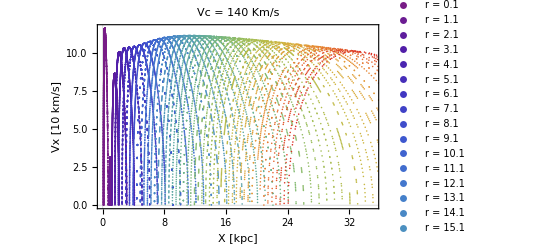

```mathematica
SetOptions[ListPlot,BaseStyle->{FontSize->14}];
ListPlot[PS, PlotTheme->"Scientific", FrameLabel->{"X [kpc]","Vx [10 km/s]"},PlotLegends->Table["r = " <>ToString[ri],{ri,0.1,50,1}], PlotLabel->"Vc = 140 Km/s",PlotStyle->Table[ColorData["Rainbow"][i],{i,0,1,1/50}]]
```